```mathematica
Exit[]
```

```mathematica
tilt = 1;
If[tilt==1,
Χ=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\bootgap2\\Ferromagnetic.dat","Table"];
A=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\bootgap2\\Antiferromagnetic.dat","Table"];
L=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\bootgap2\\Zeeman.dat","Table"];
Subscript[Φ, p]=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\bootgap2\\PerpMagneticField.dat","Table"];
Subscript[Φ, b]=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\bootgap2\\ParMagneticField.dat","Table"];
];
If[tilt==0,
δ=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\bootgap1\\Gamma.dat","Table"];
Χ=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\bootgap1\\Ferromagnetic.dat","Table"];
A=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\bootgap1\\Antiferromagnetic.dat","Table"];
Subscript[Φ, p]=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\bootgap1\\MagneticField.dat","Table"];
]
```

```mathematica
δ=Delete[δ,2];
Χ = Delete[Χ,2];
A=Delete[A,2];
L=Delete[L,2];
Subscript[Φ, p] = Delete[Subscript[Φ, p],2];
If[tilt==1,
Subscript[Φ, b] = Delete[Subscript[Φ, b],2];
];

step=150/5;
isize=2;
jsize=1;

For[j=0,j<jsize,j++,
J=j*(step+2)+2;
Subscript[Ξ, j]={};
Subscript[Λ, j]={};
Subscript[Ε, j]={};
Subscript[λ, j]={};

Subscript[θ, j]={};
For[n=1,n≤step,n++,
Subscript[Ξ, j]=Join[Subscript[Ξ, j],Χ[[n+J,All]]];
Subscript[Λ, j]=Join[Subscript[Λ, j],Subscript[Φ, p][[n+J,All]]];
Subscript[Ε, j]=Join[Subscript[Ε, j],A[[n+J,All]]];
Subscript[θ, j]=Join[Subscript[θ, j],δ[[n+J,All]]];
Subscript[λ, j]=Join[Subscript[λ, j],L[[n+J,All]]];
];
If[tilt==1,
Subscript[Ρ, j]={};
For[n=1,n≤step,n++,
Subscript[Ρ, j]=Join[Subscript[Ρ, j],Subscript[Φ, b][[n+J,All]]];
];
];
];

For[j=0,j<jsize,j++,
For[i=0,i<isize,i++,
Subscript[Μ, i,j]={};
Subscript[Βp, i,j]={};
Subscript[Α, i,j]={};
Subscript[ℒ, i,j]={};

Subscript[D, i,j]={};
For[k=0,k<step,k++,
Subscript[Μ, i,j]=Append[Subscript[Μ, i,j],Subscript[Ξ, j][[k*(isize+1)+2+i]]];
Subscript[Βp, i,j]=Append[Subscript[Βp, i,j],Subscript[Λ, j][[k*(isize+1)+2+i]]];
Subscript[Α, i,j]=Append[Subscript[Α, i,j],Subscript[Ε, j][[k*(isize+1)+2+i]]];
Subscript[D, i,j]=Append[Subscript[D, i,j],Subscript[θ, j][[k*(isize+1)+2+i]]];
Subscript[ℒ, i,j]=Append[Subscript[ℒ, i,j],Subscript[λ, j][[k*(isize+1)+2+i]]];
];
If[tilt==1,
Subscript[Βb, i,j]={};
For[k=0,k≤(step-1),k++,
Subscript[Βb, i,j]=Append[Subscript[Βb, i,j],Subscript[Ρ, j][[k*(isize+1)+2+i]]
];
];
];
];
];

mP={};
aP={};
ΔP={};
lP={};

For[j=0,j<jsize,j++,
For[i=0,i<isize,i++,
Subscript[mp, i,j]=Table[{Subscript[Βp, i,j][[μ]],Subscript[Μ, i,j][[μ]]},{μ,1,Length[Subscript[Βp, 0,0]]}];
Subscript[ap, i,j]=Table[{Subscript[Βp, i,j][[μ]],Subscript[Α, i,j][[μ]]},{μ,1,Length[Subscript[Βp, 0,0]]}];
Subscript[Δp, i,j]=Table[{Subscript[Βp, i,j][[μ]],Subscript[D, i,j][[μ]]},{μ,1,Length[Subscript[Βp, 0,0]]}];
Subscript[lp, i,j]=Table[{Subscript[Βp, i,j][[μ]],Subscript[ℒ, i,j][[μ]]},{μ,1,Length[Subscript[Βp, 0,0]]}];

mP=Append[mP,Subscript[mp, i,j]];
aP=Append[aP,Subscript[ap, i,j]];
ΔP=Append[ΔP,Subscript[Δp, i,j]];
lP=Append[lP,Subscript[lp, i,j]];
];
];

If[tilt==1,
aΒ={};
mΒ={};
ΔΒ={};
lΒ={};
For[j=0,j<jsize,j++,
For[i=0,i<isize,i++,
Subscript[mb, i,j]=Table[{Subscript[Βb, i,j][[μ]],Subscript[Μ, i,j][[μ]]},{μ,1,Length[Subscript[Βb, 0,0]]}];
Subscript[ab, i,j]=Table[{Subscript[Βb, i,j][[μ]],Subscript[Α, i,j][[μ]]},{μ,1,Length[Subscript[Βb, 0,0]]}];
Subscript[Δb, i,j]=Table[{Subscript[Βb, i,j][[μ]],Subscript[D, i,j][[μ]]},{μ,1,Length[Subscript[Βb, 0,0]]}];
Subscript[lb, i,j]=Table[{Subscript[Βb, i,j][[μ]],Subscript[ℒ, i,j][[μ]]},{μ,1,Length[Subscript[Βb, 0,0]]}];

mΒ=Append[mΒ,Subscript[mb, i,j]];
aΒ=Append[aΒ,Subscript[ab, i,j]];
ΔΒ=Append[ΔΒ,Subscript[Δb, i,j]];
lΒ=Append[lΒ,Subscript[lb, i,j]];
];
];
];

k=mP;
For[i=1,i≤Length[aP],i++,
k=Append[k,aP[[i]]];
];
For[i=1,i≤Length[lP],i++,
k=Append[k,lP[[i]]];
];
m=mΒ;
For[i=1,i≤Length[aΒ],i++,
m=Append[m,aΒ[[i]]];
];
For[i=1,i≤Length[lΒ],i++,
m=Append[m,lΒ[[i]]];
];
```

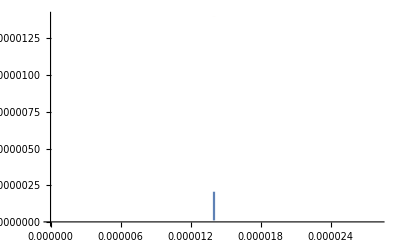

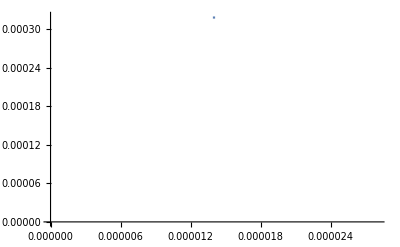

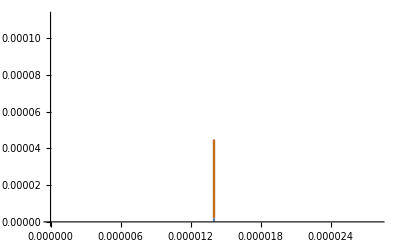

```mathematica
ListLinePlot[mP]
ListLinePlot[aP]
ListLinePlot[k]
```

```mathematica
ΔΒ11=ΔΒ[[1]];
ΔΒ12=ΔΒ[[2]];
```

```mathematica
ΔΒ31=ΔΒ[[1]];
ΔΒ32=ΔΒ[[2]];
```

```mathematica
ΔΒ51=ΔΒ[[1]];
ΔΒ52=ΔΒ[[2]];
```

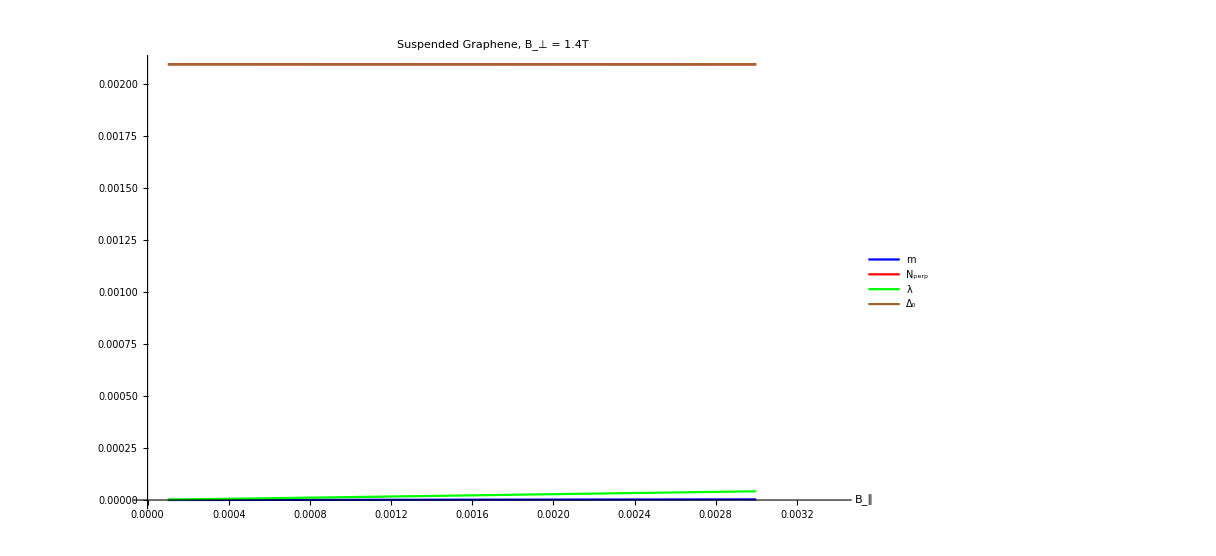

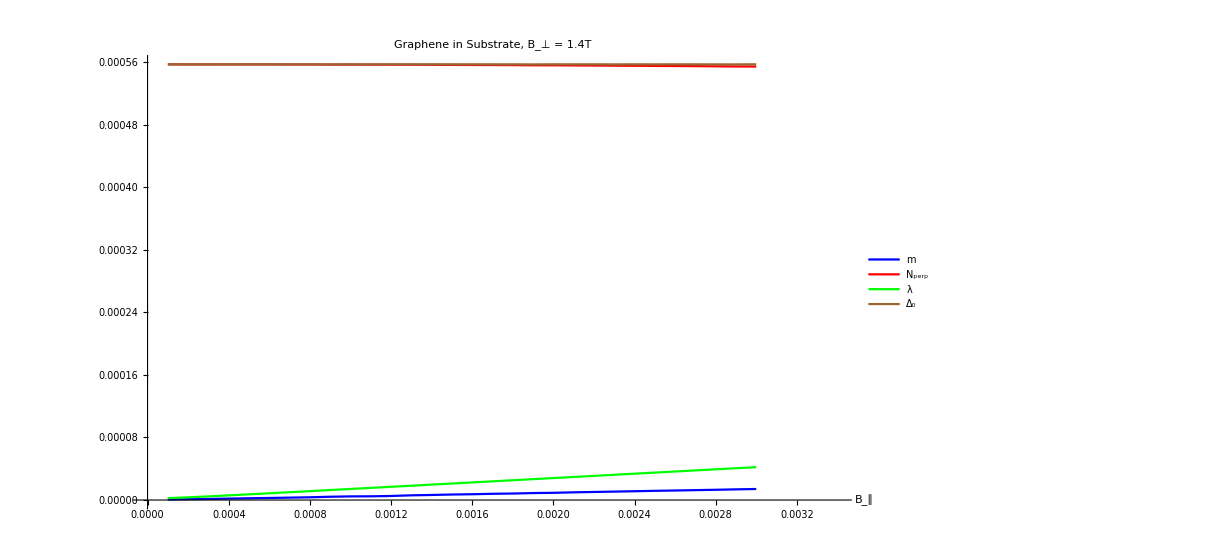

```mathematica
ListLinePlot[{m[[1]],m[[3]],m[[5]],ΔΒ[[1]]},PlotRange->{{0,0.0034},All},PlotStyle->{Blue,Red,Green,Brown},PlotLegends->Placed[{"m","N_perp","λ","Δ_0"},{Right,Bottom}],PlotLabel->"Suspended Graphene, B_⊥ = 1.4T",AxesLabel->{"B_∥",""}]
ListLinePlot[{m[[2]],m[[4]],m[[6]],ΔΒ[[2]]},PlotRange->{{0,0.0034},All},PlotStyle->{Blue,Red,Green,Brown},PlotLegends->Placed[{"m","N_perp","λ","Δ_0"},{Right,Bottom}],PlotLabel->"Graphene in Substrate, B_⊥ = 1.4T",AxesLabel->{"B_∥",""}]
```

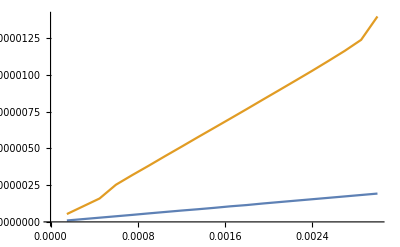

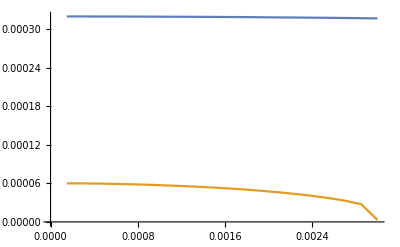

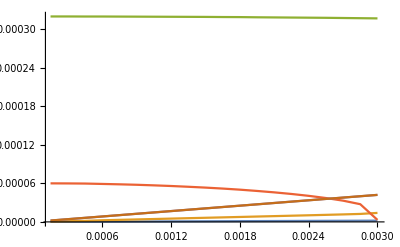

```mathematica
ListLinePlot[mΒ]
ListLinePlot[aΒ]
ListLinePlot[m,PlotRange->All]
```

```mathematica
Δ=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\bootgap2\\data.txt","Table"];
Ϟ={};
Ν={};
Ψ={};
For[i=2,i≤16,i++,
Ϟ=Append[Ϟ,Δ[[i]]];
];
For[i=19,i≤23,i++,
Ν=Append[Ν,Δ[[i]]];
];
For[i=26,i≤Length[Δ],i++,
Ψ=Append[Ψ,Δ[[i]]];
];
Ψ[[All,2]]=Ψ[[All,2]]/2;
Ð=ListPlot[{Ϟ,Ν,Ψ},PlotRange->All];

dP=ListLinePlot[ΔP,PlotRange->All];
```

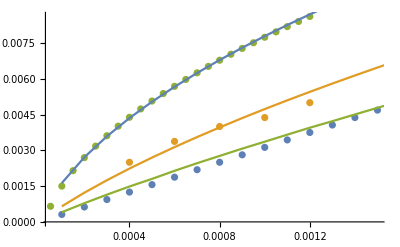

```mathematica
Show[Ð,dP]
```

```mathematica
compressYAxis[plot_,range1_,range2_]:=Module[{ytick1,ytick2,epilog1,target},ytick1=FindDivisions[range1,5]/.y_?NumericQ:>{y,y}/.{y_?NumericQ,_}/;y≥range1[[2]]:>Sequence[];
ytick2=FindDivisions[range2,5]/.y_?NumericQ:>{y-range2[[1]]+range1[[2]],y}/.{y_?NumericQ,_}/;y≤range1[[2]]:>Sequence[];
epilog=Options[plot,Epilog][[1,2]];
target=Subtract@@Reverse@range1/(Subtract@@Reverse@range1+Subtract@@Reverse@range2);
Show[plot/.{x_?NumericQ,y_?NumericQ/;y>range2[[1]]}:>{x,y-range2[[1]]+range1[[2]]},PlotRange->{range1[[1]],range1[[2]]+Subtract@@Reverse@range2},Ticks->{Automatic,Join[ytick1,ytick2]},Epilog->Join[epilog,{White,Rectangle[Scaled[{-0.1,0.98 target}],Scaled[{1.1,1.02 target}]],Black,Text[Rotate["\\",π/2],Scaled[{0,0.98 target}],{-1.5,0}],Text[Rotate["\\",π/2],Scaled[{0,1.02 target}],{-1.5,0}]}]]]
```

```mathematica
nsize=step*1;
γ=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\edgestates\\ZigzagGap1_substrate.dat","Table"];
For[n=1,n≤nsize+1,n++,
γ=Delete[γ,n];
]
ω=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\edgestates\\ZigzagGap1_suspend.dat","Table"];
For[n=1,n≤nsize+1,n++,
ω=Delete[ω,n];
]
```

```mathematica
nsize=step*1;
γ=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\edgestates\\ZigzagGap1_substrate.dat","Table"];
For[n=1,n≤nsize+1,n++,
γ=Delete[γ,n];
]
ω=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\edgestates\\ZigzagGap1_suspend.dat","Table"];
For[n=1,n≤nsize+1,n++,
ω=Delete[ω,n];
]
υ=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\edgestates\\ZigzagGap3_substrate.dat","Table"];
For[n=1,n≤nsize+1,n++,
υ=Delete[υ,n];
]
ℼ=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\edgestates\\ZigzagGap3_suspend.dat","Table"];
For[n=1,n≤nsize+1,n++,
ℼ=Delete[ℼ,n];
]
κ=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\edgestates\\ZigzagGap5_substrate.dat","Table"];
For[n=1,n≤nsize+1,n++,
κ=Delete[κ,n];
]
φ=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\edgestates\\ZigzagGap5_suspend.dat","Table"];
For[n=1,n≤nsize+1,n++,
φ=Delete[φ,n];
]
```

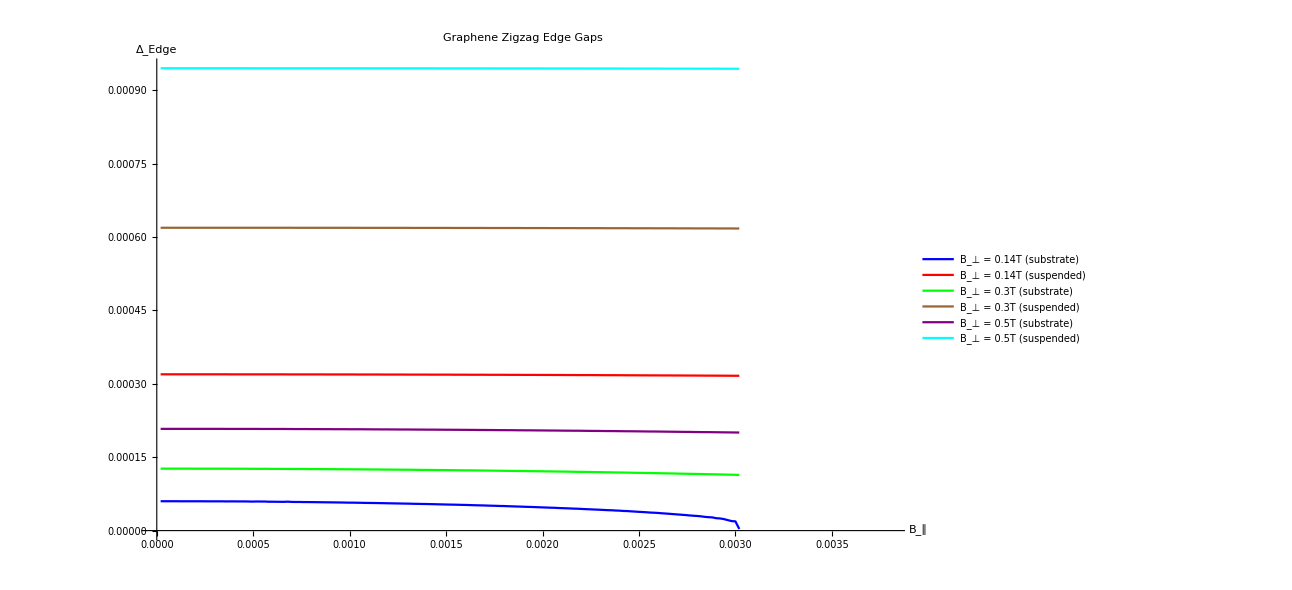

```mathematica
ListLinePlot[{γ,ω,υ,ℼ,κ,φ},PlotRange->{{0,0.0038},All},PlotStyle->{Blue,Red,Green,Brown,Purple,Cyan},PlotLegends->Placed[{"B_⊥ = 0.14T (substrate)","B_⊥ = 0.14T (suspended)","B_⊥ = 0.3T (substrate)","B_⊥ = 0.3T (suspended)","B_⊥ = 0.5T (substrate)","B_⊥ = 0.5T (suspended)"},{Right,Bottom}],AxesLabel->{"B_∥","Δ_Edge"},PlotLabel->"Graphene Zigzag Edge Gaps"]
```

```mathematica
ksize=500;
LL1=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\edgestates\\ZigzagLL+_B1.dat","Table"];
For[n=1,n≤ksize+1,n++,
LL1=Delete[LL1,n];
]
ll1=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\edgestates\\ZigzagLL-_B1.dat","Table"];
For[n=1,n≤ksize+1,n++,
ll1=Delete[ll1,n];
]
LL2=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\edgestates\\ZigzagLL+_B2.dat","Table"];
For[n=1,n≤ksize+1,n++,
LL2=Delete[LL2,n];
]
ll2=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\edgestates\\ZigzagLL-_B2.dat","Table"];
For[n=1,n≤ksize+1,n++,
ll2=Delete[ll2,n];
]
LL3=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\edgestates\\ZigzagLL+_B3.dat","Table"];
For[n=1,n≤ksize+1,n++,
LL3=Delete[LL3,n];
]
ll3=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\edgestates\\ZigzagLL-_B3.dat","Table"];
For[n=1,n≤ksize+1,n++,
ll3=Delete[ll3,n];
]
LL4=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\edgestates\\ZigzagLL+_B4.dat","Table"];
For[n=1,n≤ksize+1,n++,
LL4=Delete[LL4,n];
]
ll4=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\edgestates\\ZigzagLL-_B4.dat","Table"];
For[n=1,n≤ksize+1,n++,
ll4=Delete[ll4,n];
]
```

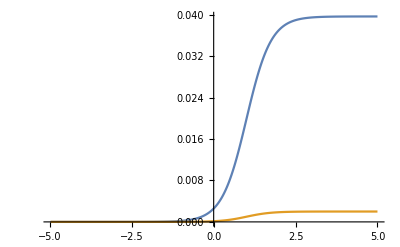

```mathematica
ksize=500;
Ν=Import["/home/chenc111/Research/c++/edgestates/Armchair_Renormed_Antif.dat","Table"];
For[n=1,n≤ksize+1,n++,
Ν=Delete[Ν,n];
]
𝓂=Import["/home/chenc111/Research/c++/edgestates/Armchair_Renormed_Ferr.dat","Table"];
For[n=1,n≤ksize+1,n++,
𝓂=Delete[𝓂,n];
]
ListLinePlot[{Ν,𝓂},PlotRange->All]
```

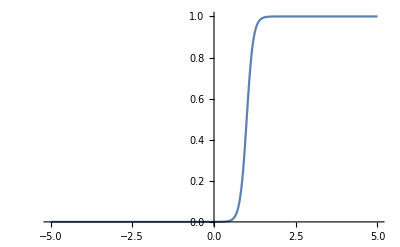

```mathematica
Plot[(1-Tanh[(-x+1)/0.2])/2,{x,-5,5}]
```

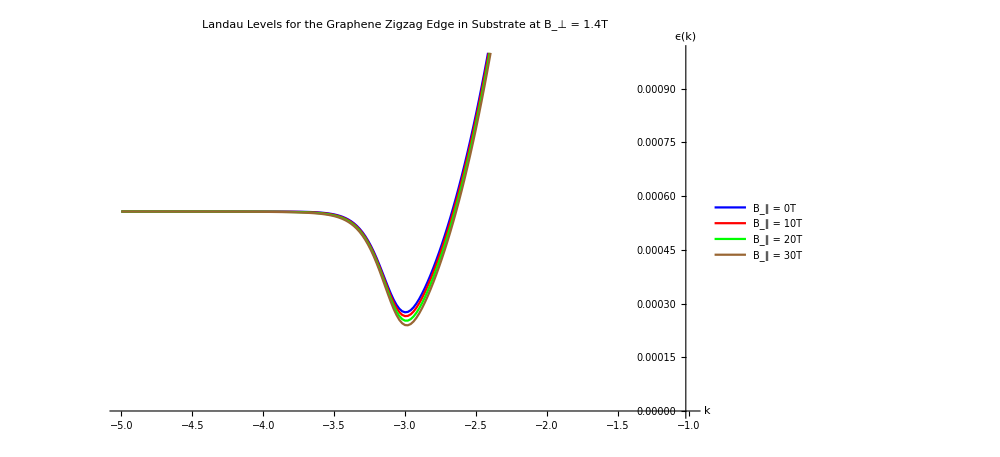

```mathematica
ListLinePlot[{ll1,ll2,ll3,ll4},PlotRange->{{-5,-1},{0,0.001}},PlotStyle->{Blue,Red,Green,Brown},PlotLegends->Placed[{"B_∥ = 0T","B_∥ = 10T","B_∥ = 20T","B_∥ = 30T"},{Left,Bottom}],PlotLabel->"Landau Levels for the Graphene Zigzag Edge in Substrate at B_⊥ = 1.4T",AxesLabel->{"k","ϵ(k)"}]
```

```mathematica
Min[ll4[[All,2]]]
```

0.0000188242

```mathematica
ll4[[96]]
```

{-3.1,0.000133672}

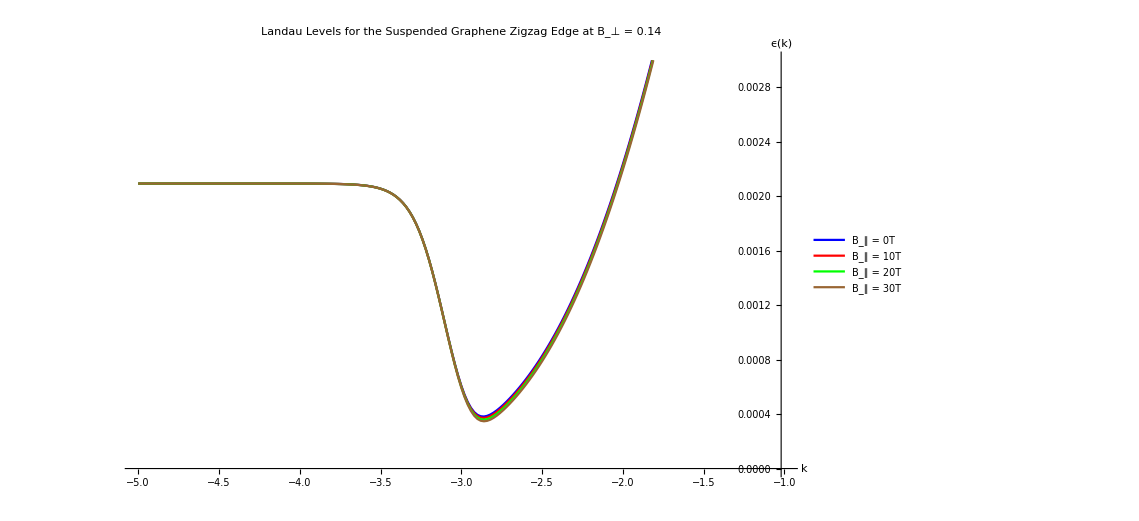

```mathematica
ListLinePlot[{LL1,LL2,LL3,LL4},PlotRange->{{-5,-1},{0,0.003}},PlotStyle->{Blue,Red,Green,Brown},PlotLegends->Placed[{"B_∥ = 0T","B_∥ = 10T","B_∥ = 20T","B_∥ = 30T"},{Left,Bottom}],PlotLabel->"Landau Levels for the Suspended Graphene Zigzag Edge at B_⊥ = 0.14",AxesLabel->{"k","ϵ(k)"}]
```

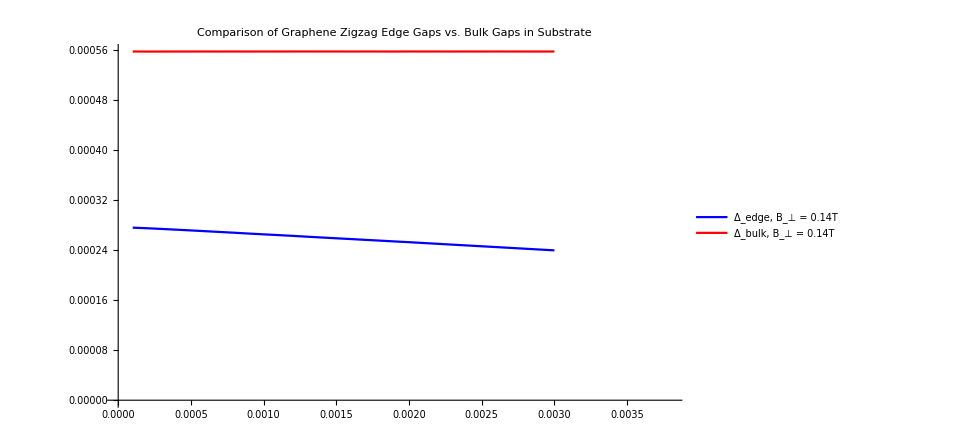

```mathematica
ListLinePlot[{γ,ΔΒ12},PlotRange->{{0,0.0038},All},PlotStyle->{Blue,Red},PlotLegends->Placed[{"Δ_edge, B_⊥ = 0.14T","Δ_bulk, B_⊥ = 0.14T"},{Right,Bottom}],PlotLabel->"Comparison of Graphene Zigzag Edge Gaps vs. Bulk Gaps in Substrate"]
```

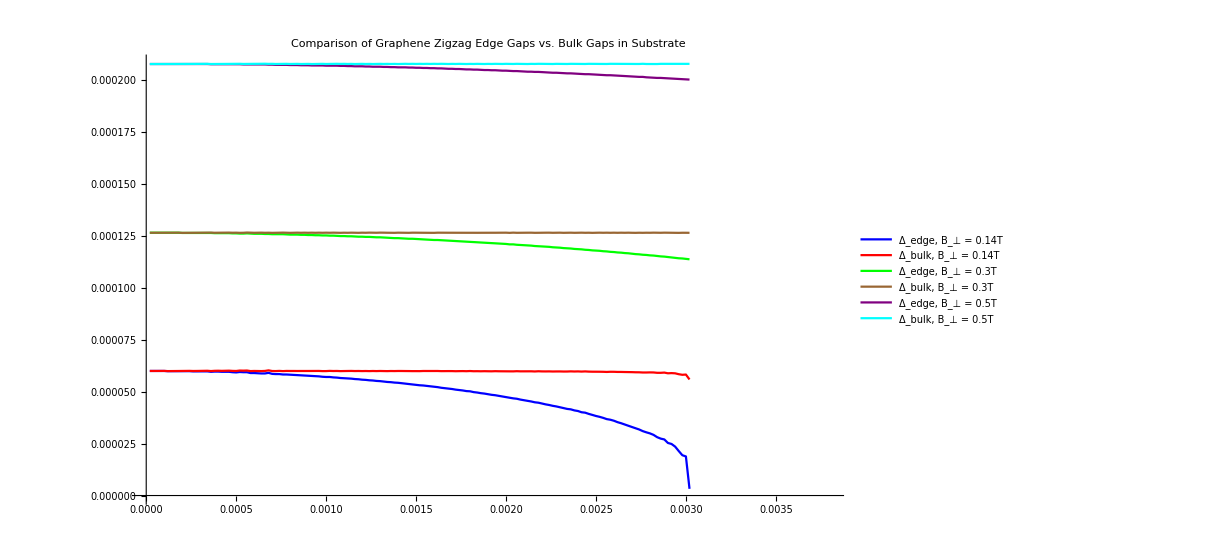

```mathematica
ListLinePlot[{γ,ΔΒ12,υ,ΔΒ32,κ,ΔΒ52},PlotRange->{{0,0.0038},All},PlotStyle->{Blue,Red,Green,Brown,Purple,Cyan},PlotLegends->Placed[{"Δ_edge, B_⊥ = 0.14T","Δ_bulk, B_⊥ = 0.14T","Δ_edge, B_⊥ = 0.3T","Δ_bulk, B_⊥ = 0.3T","Δ_edge, B_⊥ = 0.5T","Δ_bulk, B_⊥ = 0.5T"},{Right,Bottom}],PlotLabel->"Comparison of Graphene Zigzag Edge Gaps vs. Bulk Gaps in Substrate"]
```

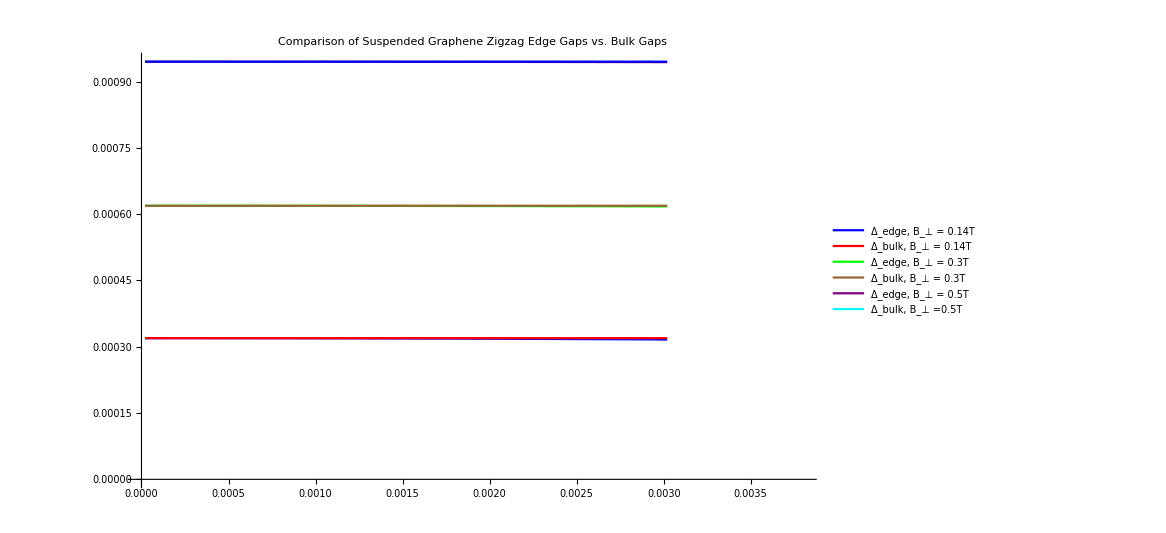

```mathematica
ListLinePlot[{ω,ΔΒ11,ℼ,ΔΒ31,φ,,ΔΒ51},PlotRange->{{0,0.0038},All},PlotStyle->{Blue,Red,Green,Brown,Purple,Cyan},PlotLegends->Placed[{"Δ_edge, B_⊥ = 0.14T","Δ_bulk, B_⊥ = 0.14T","Δ_edge, B_⊥ = 0.3T","Δ_bulk, B_⊥ = 0.3T","Δ_edge, B_⊥ = 0.5T","Δ_bulk, B_⊥ =0.5T"},{Right,Bottom}],PlotLabel->"Comparison of Suspended Graphene Zigzag Edge Gaps vs. Bulk Gaps"]
```

```mathematica
nsize=step;
γ=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\edgestates\\ArmChairGap1_substrate.dat","Table"];
For[n=1,n≤nsize+1,n++,
γ=Delete[γ,n];
]
ψ=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\edgestates\\ArmChairGap1_suspend.dat","Table"];
For[n=1,n≤nsize+1,n++,
ψ=Delete[ψ,n];
]
κ=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\edgestates\\ArmChairGap3_substrate.dat","Table"];
For[n=1,n≤nsize+1,n++,
κ=Delete[κ,n];
]
ℼ=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\edgestates\\ArmChairGap3_suspend.dat","Table"];
For[n=1,n≤nsize+1,n++,
ℼ=Delete[ℼ,n];
]
φ=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\edgestates\\ArmChairGap5_substrate.dat","Table"];
For[n=1,n≤nsize+1,n++,
φ=Delete[φ,n];
]
ι=Import["C:\\Users\\user101111001\\Desktop\\Research\\c++\\edgestates\\ArmChairGap5_suspend.dat","Table"];
For[n=1,n≤nsize+1,n++,
ι=Delete[ι,n];
]
```

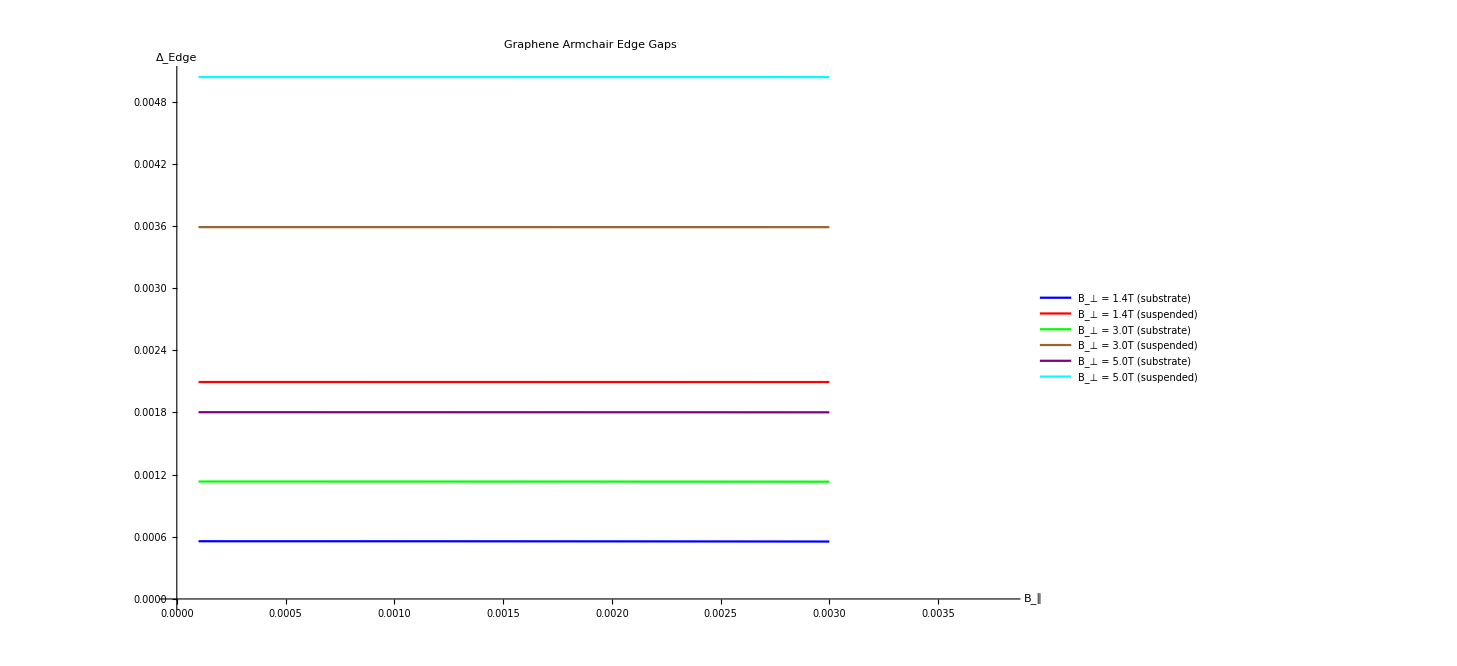

```mathematica
ListLinePlot[{γ,ψ,κ,ℼ,φ,ι},PlotRange->{{0,0.0038},All},PlotStyle->{Blue,Red,Green,Brown,Purple,Cyan},PlotLegends->Placed[{"B_⊥ = 1.4T (substrate)","B_⊥ = 1.4T (suspended)","B_⊥ = 3.0T (substrate)","B_⊥ = 3.0T (suspended)","B_⊥ = 5.0T (substrate)","B_⊥ = 5.0T (suspended)"},{Right,Bottom}],AxesLabel->{"B_∥","Δ_Edge"},PlotLabel->"Graphene Armchair Edge Gaps"]
```

```mathematica
ksize=500;
LL1=Import["/home/chenc111/Research/c++/edgestates/ArmChairLL+_B1.dat","Table"];
For[n=1,n≤ksize+1,n++,
LL1=Delete[LL1,n];
]
ll1=Import["/home/chenc111/Research/c++/edgestates/ArmChairLL-_B1.dat","Table"];
For[n=1,n≤ksize+1,n++,
ll1=Delete[ll1,n];
]
LL2=Import["/home/chenc111/Research/c++/edgestates/ArmChairLL+_B2.dat","Table"];
For[n=1,n≤ksize+1,n++,
LL2=Delete[LL2,n];
]
ll2=Import["/home/chenc111/Research/c++/edgestates/ArmChairLL-_B2.dat","Table"];
For[n=1,n≤ksize+1,n++,
ll2=Delete[ll2,n];
]
LL3=Import["/home/chenc111/Research/c++/edgestates/ArmChairLL+_B3.dat","Table"];
For[n=1,n≤ksize+1,n++,
LL3=Delete[LL3,n];
]
ll3=Import["/home/chenc111/Research/c++/edgestates/ArmChairLL-_B3.dat","Table"];
For[n=1,n≤ksize+1,n++,
ll3=Delete[ll3,n];
]
LL4=Import["/home/chenc111/Research/c++/edgestates/ArmChairLL+_B4.dat","Table"];
For[n=1,n≤ksize+1,n++,
LL4=Delete[LL4,n];
]
ll4=Import["/home/chenc111/Research/c++/edgestates/ArmChairLL-_B4.dat","Table"];
For[n=1,n≤ksize+1,n++,
ll4=Delete[ll4,n];
]
```

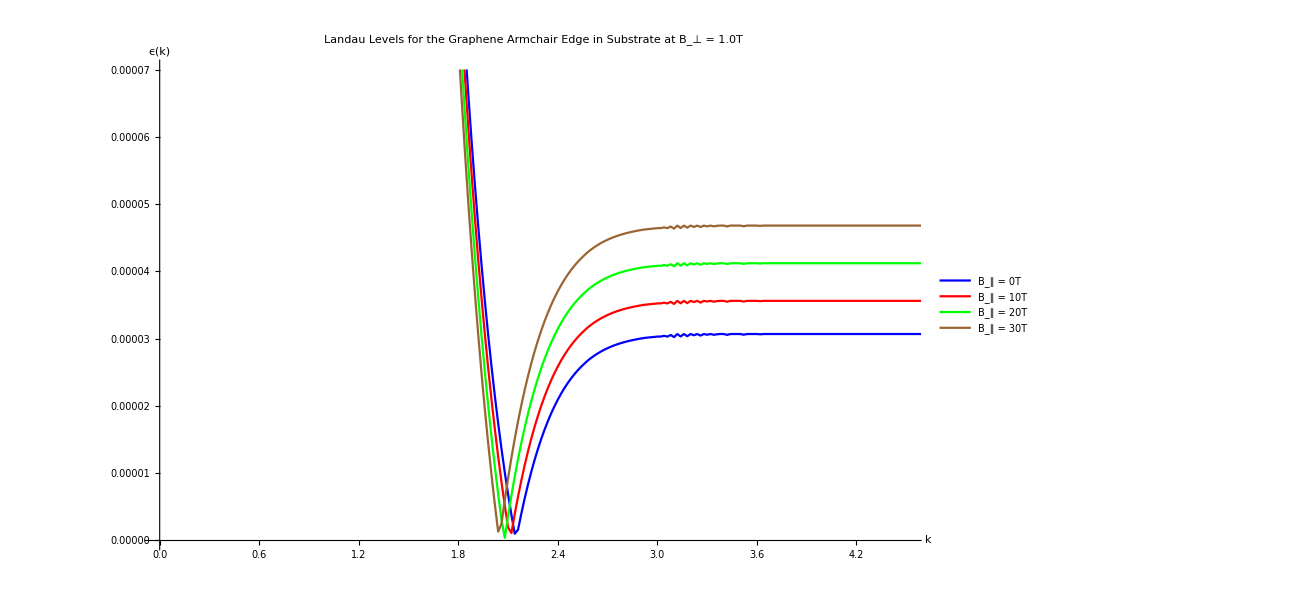

```mathematica
ListLinePlot[{ll1,ll2,ll3,ll4},PlotRange->{{0,4.5},{0,0.00007}},PlotStyle->{Blue,Red,Green,Brown},PlotLegends->Placed[{"B_∥ = 0T","B_∥ = 10T","B_∥ = 20T","B_∥ = 30T"},{Left,Bottom}],PlotLabel->"Landau Levels for the Graphene Armchair Edge in Substrate at B_⊥ = 1.0T",AxesLabel->{"k","ϵ(k)"}]
```

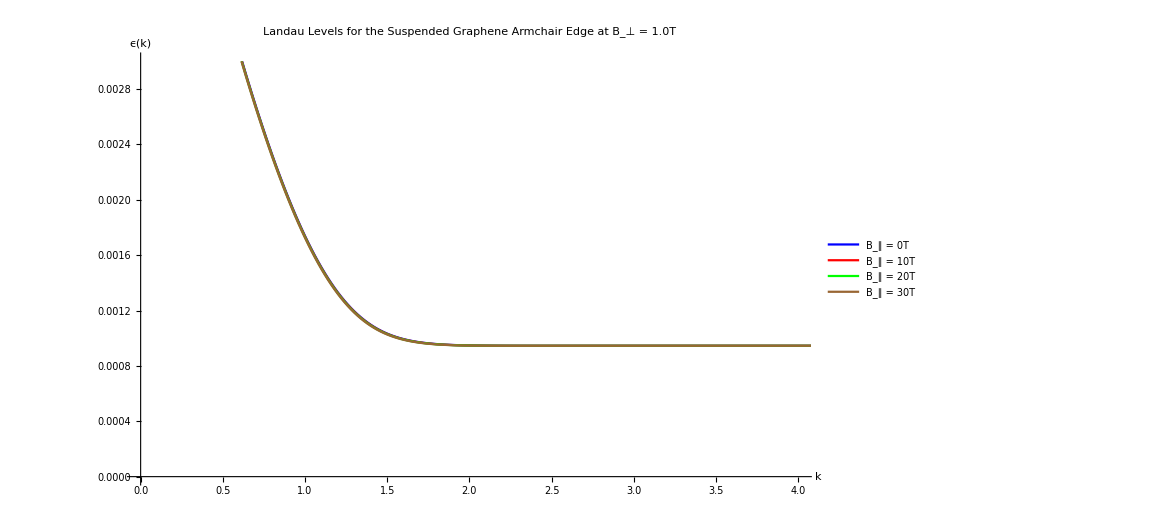

```mathematica
ListLinePlot[{LL1,LL2,LL3,LL4},PlotRange->{{0,4},{0,0.003}},PlotStyle->{Blue,Red,Green,Brown},PlotLegends->Placed[{"B_∥ = 0T","B_∥ = 10T","B_∥ = 20T","B_∥ = 30T"},{Left,Bottom}],PlotLabel->"Landau Levels for the Suspended Graphene Armchair Edge at B_⊥ = 1.0T",AxesLabel->{"k","ϵ(k)"}]
```

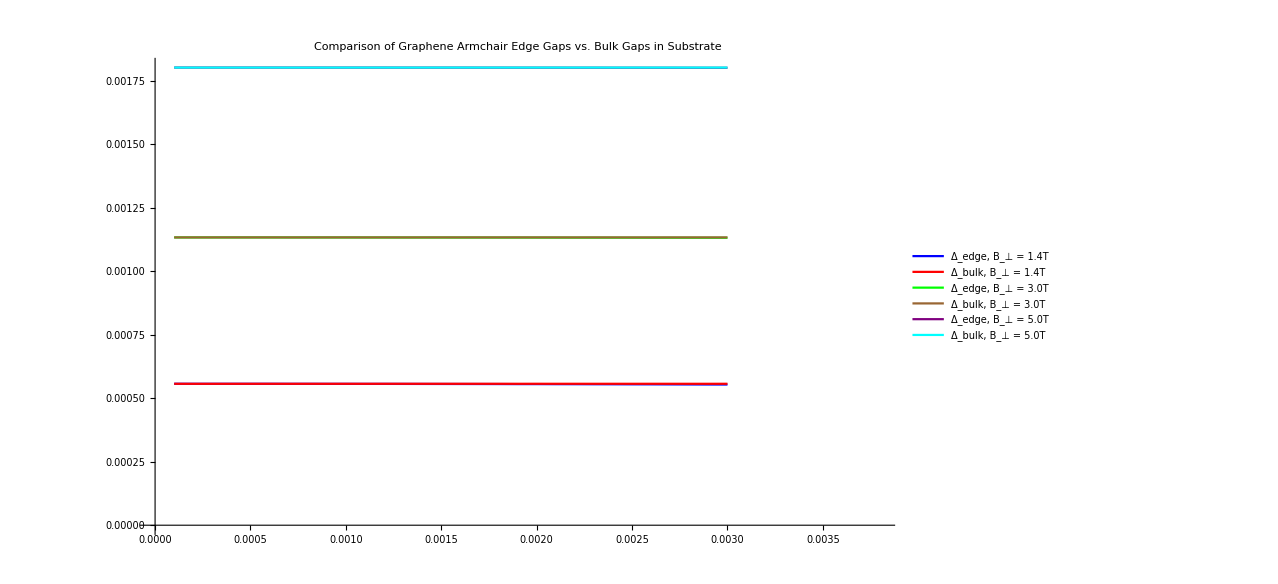

```mathematica
ListLinePlot[{γ,ΔΒ12,κ,ΔΒ32,φ,ΔΒ52},PlotRange->{{0,0.0038},All},PlotStyle->{Blue,Red,Green,Brown,Purple,Cyan},PlotLegends->Placed[{"Δ_edge, B_⊥ = 1.4T","Δ_bulk, B_⊥ = 1.4T","Δ_edge, B_⊥ = 3.0T","Δ_bulk, B_⊥ = 3.0T","Δ_edge, B_⊥ = 5.0T","Δ_bulk, B_⊥ = 5.0T"},{Right,Bottom}],PlotLabel->"Comparison of Graphene Armchair Edge Gaps vs. Bulk Gaps in Substrate"]
```

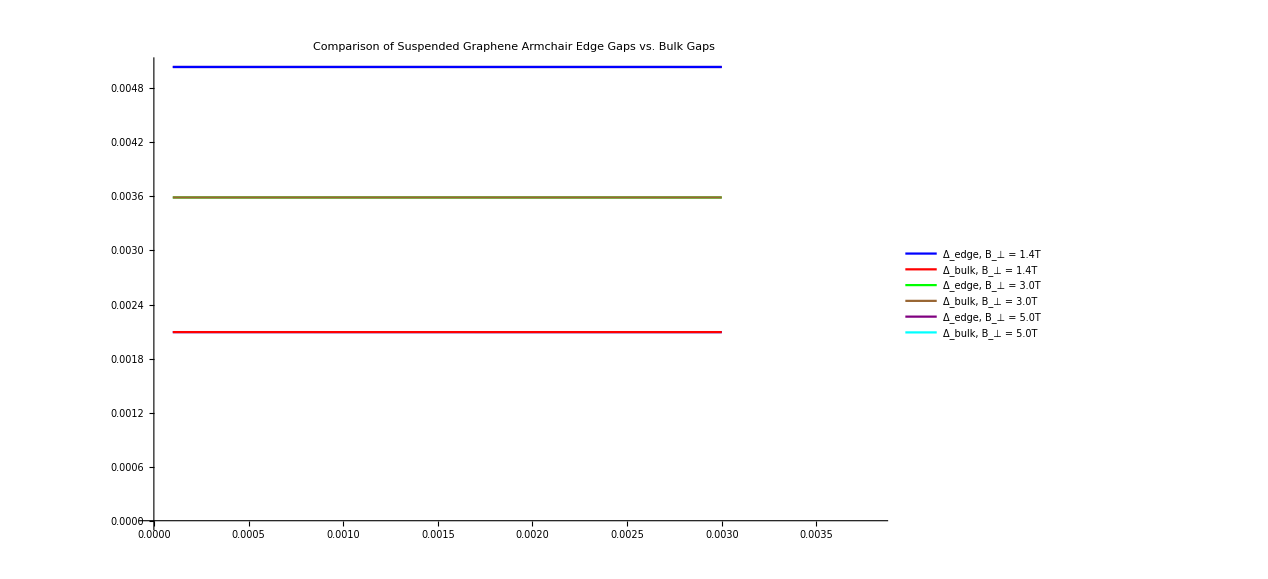

```mathematica
ListLinePlot[{ψ,ΔΒ11,ℼ,ΔΒ31,ι,,ΔΒ51},PlotRange->{{0,0.0038},All},PlotStyle->{Blue,Red,Green,Brown,Purple,Cyan},PlotLegends->Placed[{"Δ_edge, B_⊥ = 1.4T","Δ_bulk, B_⊥ = 1.4T","Δ_edge, B_⊥ = 3.0T","Δ_bulk, B_⊥ = 3.0T","Δ_edge, B_⊥ = 5.0T","Δ_bulk, B_⊥ = 5.0T"},{Right,Bottom}],PlotLabel->"Comparison of Suspended Graphene Armchair Edge Gaps vs. Bulk Gaps"]
```

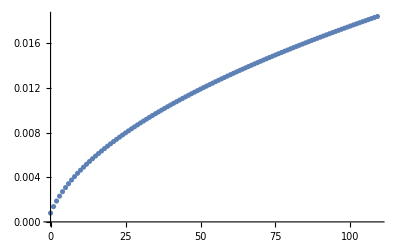

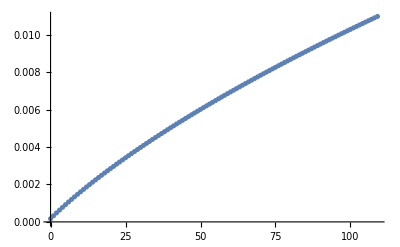

```mathematica
A=Import["/home/chenc111/Research/c++/bootgap2/AntiFerro0.1.dat","Table"];
A=Delete[A,{{1},{2},{3}}];
A1=Table[{A[[i,1]],A[[i,2]]},{i,1,Length[A]}];
A2=Table[{A[[i,1]],A[[i,3]]},{i,1,Length[A]}];
ListPlot[A1]
ListPlot[A2]
```

```mathematica
m=Import["/home/chenc111/Research/c++/bootgap2/Ferro0.1.dat","Table"];
m=Delete[m,{{1},{2},{3}}];
m1=Table[{m[[i,1]],A[[i,2]]},{i,1,Length[m]}];
m2=Table[{m[[i,1]],A[[i,3]]},{i,1,Length[m]}];
ListPlot[m1]
ListPlot[m2]
```

-Graphics-

-Graphics-